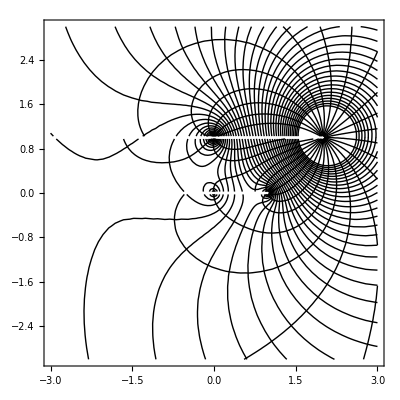

```mathematica
DrawIsoLines [debit_ , coordinates]we= {1,2,3,-10};
coords = {{0,0},{1,0},{0,1},{2,1}};
w[z_]=0;
For[i=1,i<=Length[we],i++,w[z_]=w[z]+we[[i]]/(2π)*Log[z-(coords[[i,1]]+I*coords[[i,2]])]]
phi[z_]=Re[w[z]];
psi[z_]=Im[w[z]];
g1=ContourPlot[phi[x+I*y],{x,-3,3},{y,-3,3},PlotLegends->Automatic, Contours->50,ContourShading->None];
g2=ContourPlot[psi[x+I*y],{x,-3,3},{y,-3,3},PlotLegends->Automatic, Contours->30,ContourShading->None];
Show[g1,g2]
```